-Graphics3D-

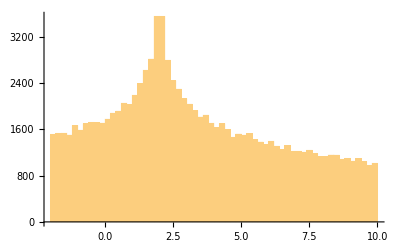

3.32663

```mathematica
makeRotationMatrix[num_]:=Table[Orthogonalize[RandomVariate[NormalDistribution[],{3,3}]],num];
rotations=makeRotationMatrix[100000];

B0vector={0,0,1.};
ListPointPlot3D[#.B0vector&/@rotations,BoxRatios->1]

csaTensor=DiagonalMatrix[{-2.,2.,10.}];
csaTensorRotated=#.csaTensor.Transpose@#&/@rotations;

B0induced=#.B0vector&/@csaTensorRotated;
chemicalShift=#.B0vector&/@B0induced;

Histogram[chemicalShift,50]
Mean@chemicalShift
```